# Zestaw 1

## Zadanie 1. Działania oraz operacje na listach, podstawy

#### Definiowanie

Zdefiniować w notatniku dwie listy:

```mathematica
l1 = {a, b, c, d, e}
```

{a,b,c,d,e}

```mathematica
l2 = {1, 2, 3, 4, 5}
```

{1,2,3,4,5}

Wykonać następujące operacje na listach 𝑙1 oraz 𝑙2, a wyniki zapisać w notatniku:

#### Dodawanie, odejmowanie

```mathematica
l1+5
```

{5+a,5+b,5+c,5+d,5+e}

```mathematica
l2+5
```

{6,7,8,9,10}

```mathematica
l1+l2
```

{1+a,2+b,3+c,4+d,5+e}

```mathematica
l1-l2
```

{-1+a,-2+b,-3+c,-4+d,-5+e}

#### Mnożenie, dzielenie

```mathematica
5*l1
```

{5 a,5 b,5 c,5 d,5 e}

```mathematica
0*l1
```

{0,0,0,0,0}

```mathematica
l1*l2
```

{a,2 b,3 c,4 d,5 e}

```mathematica
l2/0.5
```

{2.,4.,6.,8.,10.}

```mathematica
l2 / (1/2)
```

{2,4,6,8,10}

```mathematica
l1/l2
```

{a,b/2,c/3,d/4,e/5}

#### Potęgowanie

```mathematica
l1^5
```

{a^5,b^5,c^5,d^5,e^5}

```mathematica
l2^5
```

{1,32,243,1024,3125}

```mathematica
l1^l2
```

{a,b^2,c^3,d^4,e^5}

```mathematica
l1^0
```

{1,1,1,1,1}

#### Inne

```mathematica
l1.l2
```

a+2 b+3 c+4 d+5 e

```mathematica
Sqrt[l1]
```

{√a,√b,√c,√d,√e}

```mathematica
Sqrt[l2]
```

{1,√2,√3,2,√5}

```mathematica
Sqrt[N[l2]]
```

{1.,1.41421,1.73205,2.,2.23607}

```mathematica
N[Sqrt[l2]]
```

{1.,1.41421,1.73205,2.,2.23607}

```mathematica
Exp[l2]
```

{ⅇ,ⅇ^2,ⅇ^3,ⅇ^4,ⅇ^5}

```mathematica
N[Exp[l2], 50]
```

{2.7182818284590452353602874713526624977572470937,7.3890560989306502272304274605750078131803155705518,20.085536923187667740928529654581717896987907838554,54.598150033144239078110261202860878402790737038614,148.41315910257660342111558004055227962348766759388}

## Zadanie 2. Działania oraz operacje na listach, Total, Length

Dla list z 𝑙1 oraz 𝑙2 z poprzedniego zadania, obliczyć sumy: sum1 = Total[𝑙1] oraz sum2 = Total[𝑙2]

```mathematica
sum1=Total[l1]
```

a+b+c+d+e

```mathematica
sum2=Total[l2]
```

15

A następnie sprawdzić długość 𝑙1, 𝑙2, sum1 oraz sum2 przy użyciu funkcji Length[… ].

```mathematica
Map[Length, {l1, l2, sum1, sum2}]
```

{5,5,5,0}

Jaki był wynik? Zapisać w komentarzu wytłumaczenie, w tym celu zapoznać się z opisem funkcji Length[… ].

```mathematica
?Length
```

Find the number of terms in a polynomial:

```mathematica
Length[1+x+x^2+x^9]
```

4

Dla wielomianu, Length[… ] zwraca liczę składników sumy

## Zadanie 3. Działania oraz operacje na listach, Range

Wypisać listy zawierające następujące elementy korzystając z funkcji Range:

```mathematica
?Range
```

#### 1) kolejne liczby naturalne od 1 do 25

```mathematica
Range[1, 25]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25}

#### 2) kolejne liczby całkowite od −20 do 20

```mathematica
Range[-20, 20]
```

{-20,-19,-18,-17,-16,-15,-14,-13,-12,-11,-10,-9,-8,-7,-6,-5,-4,-3,-2,-1,0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

#### 3) liczby od 0 do 1, co 1/10

```mathematica
Range[0, 1, 1/10]
```

{0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1}

#### 4) liczby od 0 do 5, co 0.2

```mathematica
Range[0, 5, 0.2]
```

{0.,0.2,0.4,0.6,0.8,1.,1.2,1.4,1.6,1.8,2.,2.2,2.4,2.6,2.8,3.,3.2,3.4,3.6,3.8,4.,4.2,4.4,4.6,4.8,5.}

#### 5) liczby od 10 do 0, co −2

```mathematica
Range[10, 0, -2]
```

{10,8,6,4,2,0}

#### 6) liczby od −2𝜋 do +2𝜋, co 𝜋/4

```mathematica
Range[-2Pi, 2Pi, Pi/4]
```

{-2 π,-(7 π)/4,-(3 π)/2,-(5 π)/4,-π,-(3 π)/4,-π/2,-π/4,0,π/4,π/2,(3 π)/4,π,(5 π)/4,(3 π)/2,(7 π)/4,2 π}

#### 7) liczby od 𝑎 do 20𝑎, co 𝑎

```mathematica
Range[a, 20a, a]
```

{a,2 a,3 a,4 a,5 a,6 a,7 a,8 a,9 a,10 a,11 a,12 a,13 a,14 a,15 a,16 a,17 a,18 a,19 a,20 a}

#### Ciekawostka

Sprawdzić działanie funkcji Range[Range[10]], co uzyskujemy w wyniku?

```mathematica
Range[{1, 4, 2}]
```

{{1},{1,2,3,4},{1,2}}

```mathematica
Range[Range[10]]
```

{{1},{1,2},{1,2,3},{1,2,3,4},{1,2,3,4,5},{1,2,3,4,5,6},{1,2,3,4,5,6,7},{1,2,3,4,5,6,7,8},{1,2,3,4,5,6,7,8,9},{1,2,3,4,5,6,7,8,9,10}}

## Zadanie 4. Działania oraz operacje na listach, Part, Take, Drop, Select, EvenQ, OddQ, PrimeQ oraz inne

Zdefiniować listę 𝑙3 będącą ciągiem kolejnych liczb naturalnych od 1 do 50 przy użyciu funkcji Range, a
następnie wybrać następujące elementy listy korzystając z zaproponowanych funkcji

```mathematica
l3=Range[1, 50]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50}

### Funkcja Part, Take, Drop zapis lista[[…]]

```mathematica
?Part
```

```mathematica
?Take
```

```mathematica
?Drop
```

#### 1) pierwsze 10

```mathematica
Part[l3,;;10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
l3[[;;10]]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Take[l3, 10]
```

{1,2,3,4,5,6,7,8,9,10}

#### 2) pierwszy, trzeci, piąty

```mathematica
l3[[{1, 3, 5}]]
```

{1,3,5}

#### 3) ostatni

```mathematica
l3[[-1]]
```

50

#### 4) ostatnie 10

```mathematica
l3[[-10;;]]
```

{41,42,43,44,45,46,47,48,49,50}

```mathematica
Take[l3, -10]
```

{41,42,43,44,45,46,47,48,49,50}

#### 5) bez pierwszych 20

```mathematica
l3[[20+1;;]]
```

{21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50}

```mathematica
?Drop
```

```mathematica
Drop[l3, 20]
```

{21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50}

#### 6) wszystkie nieparzyste

```mathematica
l3[[;;;;2]]
```

{1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,49}

#### 7) wszystkie parzyste

```mathematica
l3[1;;;;2]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50}[1;;All;;2]

#### 8) od 3-go elementu do 30-go elementu, co piąty

```mathematica
l3[[3;;30;;5]]
```

{3,8,13,18,23,28}

### Funkcja Select, wybierz wszystkie

```mathematica
?Select
```

#### 9) parzyste

```mathematica
?Mod
```

```mathematica
Select[l3, EvenQ]
```

{2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,48,50}

#### 10) nieparzyste

```mathematica
Select[l3, OddQ]
```

{1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,49}

#### 11) liczby pierwsze

```mathematica
Select[l3, PrimeQ]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47}

#### 12) podzielne przez 7

```mathematica
Select[l3, n |->  Divisible[n, 7]]
```

{7,14,21,28,35,42,49}

#### 13) podzielne przez 3 oraz 7

```mathematica
Select[l3, n |-> Divisible[n, 3] && Divisible[n, 7]]
```

{21,42}

#### 14) większe od 11.5

```mathematica
Select[l3, n |->n >11.5]
```

{12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50}

#### 15) wszystkie postaci , gdzie 𝑘 ∈ ℕ

```mathematica
Select[l3, n |-> IntegerQ[CubeRoot[n + 1]]]
```

{7,26}

#### 16) takie, że silnia z elementu listy w zapisie dziesiętnym ma parzystą liczbę cyfr

```mathematica
?IntegerLength
```

```mathematica
Select[l3, n |-> EvenQ[IntegerLength[n!, 10]]]
```

{4,7,9,11,13,16,18,19,21,22,24,25,28,31,32,36,37,40,41,42,46,47,48}

## Zadanie 5. Rzut kostkami, Mean, StandardDeviation, Histogram, Count oraz inne

Zasymulować eksperyment z dwiema standardowym kostkami 6-ściennymi, 𝐴 oraz 𝐵. Wygenerować
używając funkcji RandomInteger, po 𝑛 = 100 wyników rzutów dla kostki 𝐴 oraz osobno dla kostki 𝐵.

```mathematica
SeedRandom[1410]
```

RandomGeneratorState[…]

```mathematica
?RandomInteger
```

```mathematica
RollTheDice=numberOfDices |-> RandomInteger[{1, 6}, numberOfDices]
```

Function[numberOfDices,RandomInteger[{1,6},numberOfDices]]

Wyniki rzutów zapisać odpowiednio jako lista 𝑙𝐴 oraz lista 𝑙𝐵.

```mathematica
lA=RollTheDice[100]
```

{6,6,4,6,3,1,1,6,6,5,3,6,4,4,2,5,6,3,2,4,6,3,4,4,1,1,5,4,1,2,1,5,4,6,5,4,2,4,3,2,4,3,6,4,4,6,4,1,5,6,1,4,5,3,1,6,6,3,4,1,1,1,1,6,1,5,4,5,4,4,5,1,5,4,6,1,5,3,4,2,1,3,4,4,1,3,2,2,6,2,4,4,1,3,1,4,1,2,6,2}

```mathematica
lB=RollTheDice[100]
```

{3,2,3,3,2,3,5,5,6,6,5,5,1,3,3,5,3,2,5,3,4,1,6,3,4,5,5,3,4,4,3,5,5,1,5,3,2,1,6,3,1,1,6,5,1,1,4,1,4,1,1,5,2,2,5,2,6,5,5,5,5,5,6,2,4,1,1,3,6,5,3,4,6,1,1,2,6,4,4,6,3,1,1,3,1,1,1,5,1,3,3,2,1,6,4,5,4,5,2,5}

Zdefiniować listę zawierającą sumy wyników na obu kostkach w kolejnych rzutach, tj. 𝑙𝐴𝐵 = 𝑙𝐵 + 𝑙𝐵.

```mathematica
lAB=lA+lB
```

{9,8,7,9,5,4,6,11,12,11,8,11,5,7,5,10,9,5,7,7,10,4,10,7,5,6,10,7,5,6,4,10,9,7,10,7,4,5,9,5,5,4,12,9,5,7,8,2,9,7,2,9,7,5,6,8,12,8,9,6,6,6,7,8,5,6,5,8,10,9,8,5,11,5,7,3,11,7,8,8,4,4,5,7,2,4,3,7,7,5,7,6,2,9,5,9,5,7,8,7}

Następnie:

### 1) obliczyć wartość średnią z 𝑙𝐴𝐵

```mathematica
Mean[N[lAB]]
```

6.92

### 2) obliczyć odchylenie standardowe z 𝑙𝐴𝐵

(1/(n-1)∑_(i=1)^n (x_i-μ̂)^2)^(1/2)

```mathematica
StandardDeviation[N[lAB]]
```

2.38971

### 3) sprawdzić jak wartość średnia z 𝑙𝐴𝐵 zmienia się wraz ze wzrostem liczby rzutów 𝑛 do oraz .

Operować na wartościach numerycznych, jaka jest szacunkowa dokładność wyniku?

```mathematica
multipleDiceRolls = Map[RollTheDice, {100, 10^4, 10^6}]
```

```mathematica
Map[rolls |-> Mean[N[rolls]], multipleDiceRolls]
```

{3.45,3.4883,3.49934}

Porównać wynik z wartością odchylenia standardowego z 𝑙𝐴𝐵 podzieloną przez .

```mathematica
Map[rolls |-> StandardDeviation[N[rolls]] / Sqrt[Length[rolls]], multipleDiceRolls]
```

{0.174295,0.0171481,0.00170694}

### 4) dla przedstawić wartości 𝑙𝐴𝐵 na wykresie tak by można było odczytać prawdopodobieństwo uzyskania poszczególnych wartości, 2, 3, ..., 12.

```mathematica
n=10^4
```

10000

```mathematica
lAB= RollTheDice[n] + RollTheDice[n]
```

```mathematica
counts = Counts[lAB]
```

<|4→801,8→1375,6→1463,12→269,2→263,5→1150,9→1105,10→876,7→1666,3→509,11→523|>

```mathematica
keys = Sort[Keys[counts]]
```

{2,3,4,5,6,7,8,9,10,11,12}

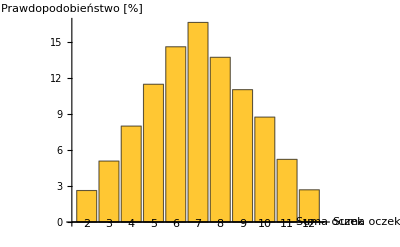

```mathematica
BarChart[
Map[key |-> Labeled[100 * N[counts[key]] / n, key], keys],
AxesLabel->{"Suma oczek","Prawdopodobieństwo [%]"}
]
```

### 5) jaka jest szansa (prawdopodobieństwo) na wyrzucenie:

Wskazówka: zapoznaj się z funkcją Count albo BinCounts

```mathematica
DiceCountToProbability = count |-> PercentForm[N[count] / n]
```

Function[count,N[count]/n]

#### a) 2

```mathematica
DiceCountToProbability[Count[lAB, 2]]
```

2.63%

#### b) 7

```mathematica
DiceCountToProbability[Count[lAB, 7]]
```

16.66%

#### c) 6 albo 8

```mathematica
counts = Counts[lAB]
```

<|4→801,8→1375,6→1463,12→269,2→263,5→1150,9→1105,10→876,7→1666,3→509,11→523|>

```mathematica
DiceCountToProbability[counts[6] + counts[8]]
```

28.38%

#### d) liczby nieparzystej

```mathematica
DiceCountToProbability[Total[
Map[key |-> counts[key], Select[keys, OddQ]]
]]
```

49.53%

#### e) liczby parzystej

```mathematica
DiceCountToProbability[Total[
Map[key |-> counts[key], Select[keys, EvenQ]]
]]
```

50.47%

### 6) ile wynoszą powyższe prawdopodobieństwa obliczone teoretycznie?

Można rozwiązać zadanie „na kartce” a wyniki wpisać do notatnika albo wspomóc się programem Mathematica®.

```mathematica
diceResults = Range[6]
```

{1,2,3,4,5,6}

```mathematica
dicePairs = Tuples[{diceResults, diceResults}]
```

{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{2,1},{2,2},{2,3},{2,4},{2,5},{2,6},{3,1},{3,2},{3,3},{3,4},{3,5},{3,6},{4,1},{4,2},{4,3},{4,4},{4,5},{4,6},{5,1},{5,2},{5,3},{5,4},{5,5},{5,6},{6,1},{6,2},{6,3},{6,4},{6,5},{6,6}}

```mathematica
diceSums = Map[pair |-> Total[pair], dicePairs]
```

{2,3,4,5,6,7,3,4,5,6,7,8,4,5,6,7,8,9,5,6,7,8,9,10,6,7,8,9,10,11,7,8,9,10,11,12}

```mathematica
sumCounts = Counts[diceSums]
```

<|2→1,3→2,4→3,5→4,6→5,7→6,8→5,9→4,10→3,11→2,12→1|>

```mathematica
probabilities = Map[i |-> i/Length[dicePairs], sumCounts]
```

<|2→1/36,3→1/18,4→1/12,5→1/9,6→5/36,7→1/6,8→5/36,9→1/9,10→1/12,11→1/18,12→1/36|>

```mathematica
N[probabilities]
```

<|2→0.0277778,3→0.0555556,4→0.0833333,5→0.111111,6→0.138889,7→0.166667,8→0.138889,9→0.111111,10→0.0833333,11→0.0555556,12→0.0277778|>

Jaka jest szansa (prawdopodobieństwo) na wyrzucenie:

#### a) 2

```mathematica
result = probabilities[2]
```

1/36

```mathematica
PercentForm[N[result]]
```

2.778%

#### b) 7

```mathematica
result = probabilities[7]
```

1/6

```mathematica
PercentForm[N[result]]
```

16.67%

#### c) 6 albo 8

```mathematica
result = probabilities[6] + probabilities[8]
```

5/18

```mathematica
PercentForm[N[result]]
```

27.78%

#### d) liczby nieparzystej

```mathematica
result = Total[
Map[key |-> probabilities[key], Select[keys, OddQ]]
]
```

1/2

#### e) liczby parzystej

```mathematica
result = Total[
Map[key |-> probabilities[key], Select[keys, EvenQ]]
]
```

1/2